```mathematica
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Miscellaneous`;
```

```mathematica
<<PhysicalApplications`Astrophysics`Cosmology`Kinematics`;
<<PhysicalApplications`Astrophysics`Cosmology`Kinematics`;
```

Cosmology:Kinematics: Warnings : Assumptions inherent in code only apply at relatively low redshifts z<10^9, so T<<m_e

Cosmology:Kinematics: Warnings : Assumptions inherent in code only apply at relatively low redshifts z<10^9, so T<<m_e

```mathematica
ΩM=0.3;
ΩΛ=0.7;
α=-1;
c=3*10^8;
M0=(1.989*10^30 *6.674*10^-11)/c^2;(*Unitless *)
```

```mathematica
En[z_]:=√(ΩM(1+z)^3+ΩΛ)

Pok[z_,Mc_]:=If[PracticalDistanceLuminosity[z]/(Dres(Mc/(1.2 M0))^(5/6) Mega Parsec)<1,DetectorCumulativeAngleFactorGreater["MonteCarlo"][PracticalDistanceLuminosity[z]/(Dres(Mc/(1.2 M0))^(5/6) Mega Parsec)],0]

Rv[z_]:=0.015 (1+z)^2.7/(1+((1+z)/2.9)^5.6)
```

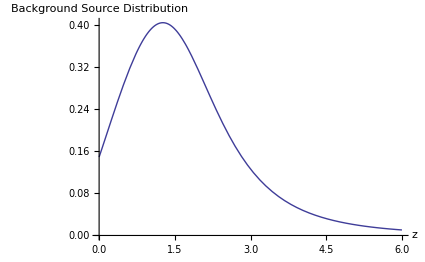

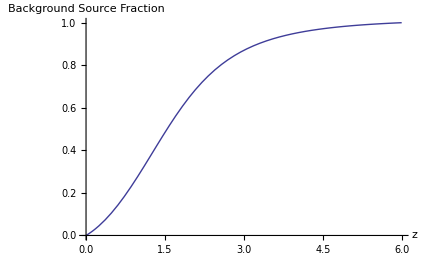

```mathematica
B0=NIntegrate[Rv[z]/((1+z)^(1/3)En[z]),{z,0,6}];

PDF0[z0_]:=Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1

Plot[PDF0[z],{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425]

Clear[P]
Clear[sol0]
sol0= P/.NDSolve[{P'[z]==PDF0[z], P[0]==0}, P,{z,0,6}][[1]];

Plot[sol0[z],{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Fraction",Black,20,Bold]},TicksStyle->15,ImageSize->425]
```

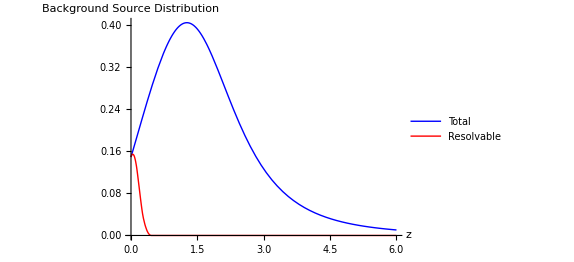

```mathematica
Dres = 440 (*# of Mega Parsecs*);

Mc = 10 M0;

B0=NIntegrate[Rv[z]/((1+z)^(1/3)En[z]),{z,0,6}];

PDF0[z0_]:=Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1
PDFp[z0_]:=(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1

Plot[{PDF0[z],PDFp[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.60}]]
```

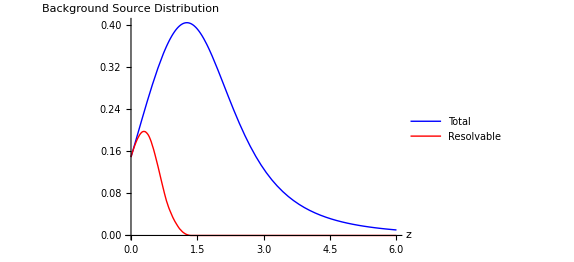

```mathematica
Dres = 440 (*# of Mega Parsecs*);

Mc = 50 M0;

B0=NIntegrate[Rv[z]/((1+z)^(1/3)En[z]),{z,0,6}];

PDF0[z0_]:=Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1
PDFp[z0_]:=(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1

Plot[{PDF0[z],PDFp[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.60}]]
```

Power::infy: Infinite expression 1/0.^1.2 encountered.

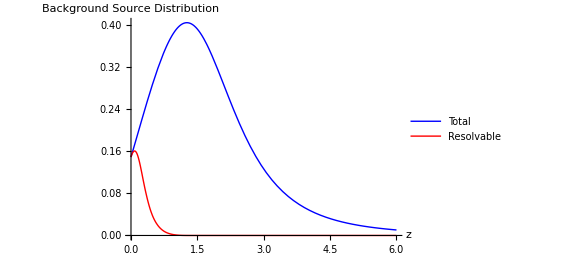

InterpolatingFunction::dmval: Input value {1.00257} lies outside the range of data in the interpolating function. Extrapolation will be used.

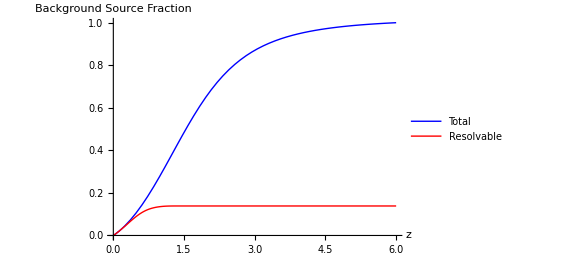

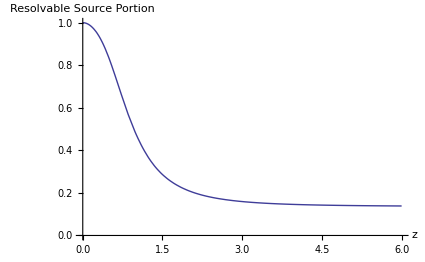

0.138647

0.138647

```mathematica
Dres = 440 (*# of Mega Parsecs*);

PDF0m[z0_]:=NIntegrate[Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]
PDFpm[z0_]:=NIntegrate[(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]

Plot[{PDF0m[z],PDFpm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Clear[P]
Clear[sol0m]
sol0m= P/.NDSolve[{P'[z]==PDF0[z], P[0]==0}, P,{z,0,6}][[1]];
Clear[P]
Clear[solzm]
solzm= P/.NDSolve[{P'[z]==PDFp[z], P[0]==0}, P,{z,0,6}][[1]];

Plot[{sol0m[z],solzm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Fraction",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1},PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Plot[{solzm[z]/sol0m[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Resolvable \n Source \n Portion",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1}]

solzm[6]/sol0m[6](*lambda*)
```

Power::infy: Infinite expression 1/0.^1.2 encountered.

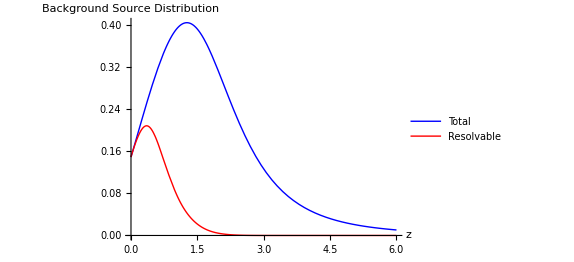

InterpolatingFunction::dmval: Input value {1.00847} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00592} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

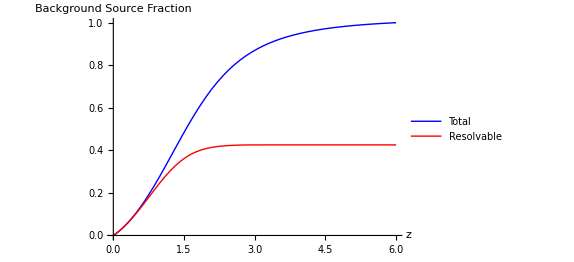

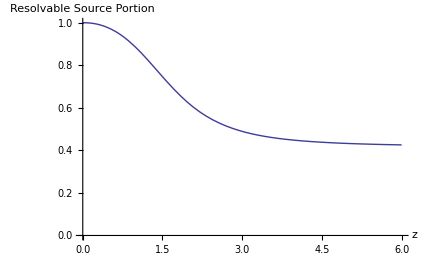

0.425706

```mathematica
Dres = 1320 (*# of Mega Parsecs*);

PDF0m[z0_]:=NIntegrate[Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]
PDFpm[z0_]:=NIntegrate[(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]

Plot[{PDF0m[z],PDFpm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Clear[P]
Clear[sol0m]
sol0m= P/.NDSolve[{P'[z]==PDF0[z], P[0]==0}, P,{z,0,6}][[1]];
Clear[P]
Clear[solzm]
solzm= P/.NDSolve[{P'[z]==PDFp[z], P[0]==0}, P,{z,0,6}][[1]];

Plot[{sol0m[z],solzm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Fraction",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1},PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Plot[{solzm[z]/sol0m[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Resolvable \n Source \n Portion",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1}]

solzm[6]/sol0m[6](*lambda*)
```

Power::infy: Infinite expression 1/0.^1.2 encountered.

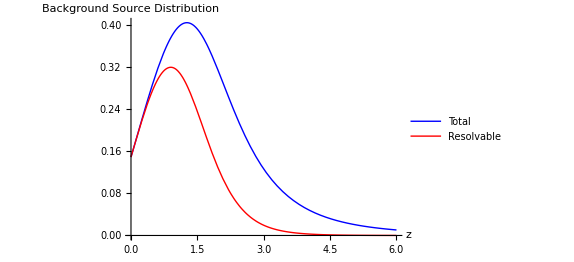

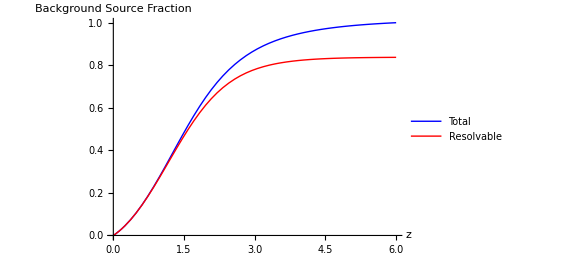

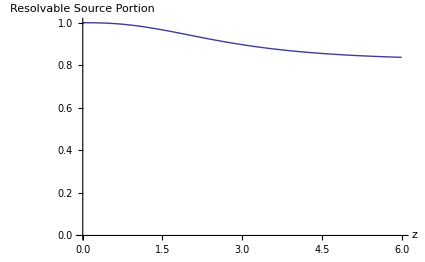

0.837187

```mathematica
Dres = 4440 (*# of Mega Parsecs*);

PDF0m[z0_]:=NIntegrate[Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]
PDFpm[z0_]:=NIntegrate[(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]

Plot[{PDF0m[z],PDFpm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Clear[P]
Clear[sol0m]
sol0m= P/.NDSolve[{P'[z]==PDF0[z], P[0]==0}, P,{z,0,6}][[1]];
Clear[P]
Clear[solzm]
solzm= P/.NDSolve[{P'[z]==PDFp[z], P[0]==0}, P,{z,0,6}][[1]];

Plot[{sol0m[z],solzm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Fraction",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1},PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Plot[{solzm[z]/sol0m[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Resolvable \n Source \n Portion",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1}]

solzm[6]/sol0m[6](*lambda*)
```

```mathematica
table={};

Do[ Dres = 440 (n+9)/10;

PDF0m[z0_]:=Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1;
PDFpm[z0_]:=NIntegrate[(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}];

Clear[P];
Clear[sol0m];
sol0m= P/.NDSolve[{P'[z]==PDF0[z], P[0]==0}, P,{z,0,6}][[1]];
Clear[P];
Clear[solzm];
solzm= P/.NDSolve[{P'[z]==PDFp[z], P[0]==0}, P,{z,0,6}][[1]];

table=Append[table,{440 (n+9)/10,solzm[6]/sol0m[6]}],{n,91}]
Print[table]
```

InterpolatingFunction::dmval: Input value {1.00257} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00204} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

$Aborted

{{440,0.138647},{484,0.153865},{528,0.169174},{572,0.184536},{616,0.199911},{660,0.215263},{704,0.230558},{748,0.245764},{792,0.260852},{836,0.275794},{880,0.290568},{924,0.305153},{968,0.31953},{1012,0.333684},{1056,0.347603},{1100,0.361275},{1144,0.374693},{1188,0.387849},{1232,0.400738},{1276,0.413358},{1320,0.425706},{1364,0.437781},{1408,0.449583},{1452,0.461114},{1496,0.472376},{1540,0.483371},{1584,0.494102},{1628,0.504573},{1672,0.514788},{1716,0.524751},{1760,0.534467},{1804,0.543941},{1848,0.553178},{1892,0.562182},{1936,0.570961},{1980,0.579518},{2024,0.587859},{2068,0.59599},{2112,0.603914},{2156,0.611641},{2200,0.619171},{2244,0.626513},{2288,0.633669},{2332,0.640647},{2376,0.647451},{2420,0.654085},{2464,0.660554},{2508,0.666863},{2552,0.673018},{2596,0.67902},{2640,0.684876}}

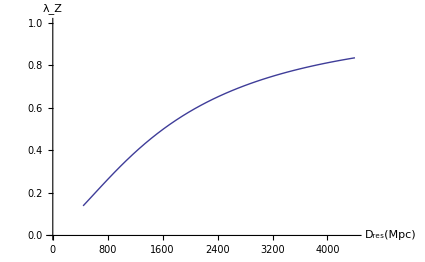

```mathematica
Plot[If[x>440,Interpolation[table][x],-10],{x,0,4400},Exclusions->x==440,AxesLabel->{Style["D_res(Mpc)",Black,20,Bold],Style["λ_Z",Black,30,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1}]
```